# Quiz 1

### Problem 1

Compute the limit x->2 for 5 x^3-4x+9

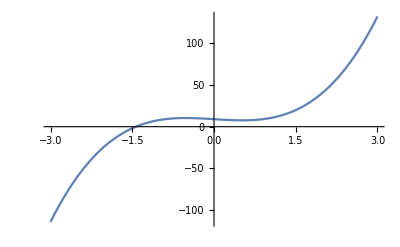

```mathematica
Plot[5 x^3-4x+9, {x,-3,3}]
```

```mathematica
5 x^3-4x+9/. x->2
```

41

```mathematica
{Limit[5 x^3-4x+9,x->2,Direction->"FromBelow"],
Limit[5 x^3-4x+9,x->2,Direction->"FromAbove"]}
```

{41,41}

```mathematica
Limit[5 x^3-4x+9,x->2]
```

41

## Problem 2

```mathematica
f[x_]:=Tan[3x]
```

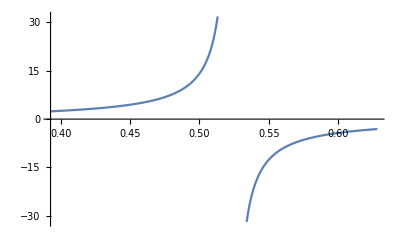

```mathematica
Plot[f[x],{x,π/8,π/5}, GridLines->{{π/6},{}}]
```

```mathematica
{Limit[f[x],x->π/6,Direction->"FromBelow"],
Limit[f[x],x->π/6,Direction->"FromAbove"]}
```

{∞,-∞}

```mathematica
Limit[f[x],x->π/6]
```

Indeterminate

## Problem 3

Domain for (3x)/(x^2+2x-15)

```mathematica
Solve[x^2+2x-15==0,x]
```

{{x→-5},{x→3}}

```mathematica
FunctionDomain[(3x)/(x^2+2x-15),x]
```

x<-5||-5<x<3||x>3

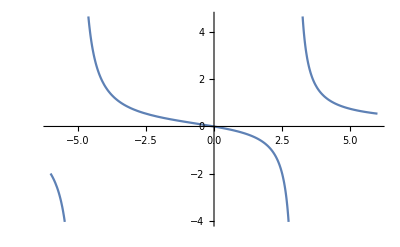

```mathematica
Plot[(3x)/(x^2+2x-15),{x,-6,6}]
```

## Problem 4

Compute the range of 21 x^7

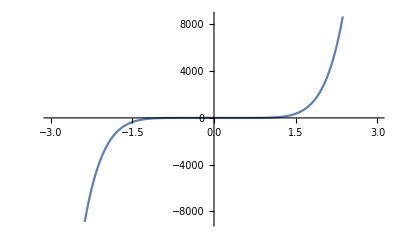

```mathematica
Plot[21 x^7,{x,-3,3}]
```

```mathematica
FunctionRange[21 x^7,x,y]
```

True

## Problem 5

```mathematica
f[x_]:=Piecewise[{{2x+4,x<1},{3 x^2,x>=1}}]
```

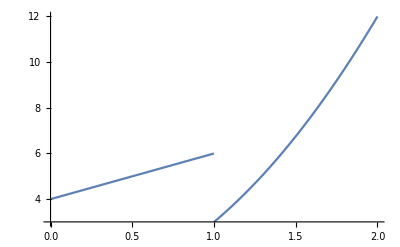

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
{Limit[f[x],x->1,Direction->"FromBelow"],
Limit[f[x],x->1,Direction->"FromAbove"]}
```

{6,3}

```mathematica
Limit[f[x],x->1]
```

Indeterminate